```mathematica
(* 拡張解析信号 *)
(* created at 2011/12/25 *)
```

```mathematica
(* 離散ユニットステップフィルタ *)
step[n_Integer?Positive]:=1+Sign[Sin[π Range[1,-1,-2/n]//Most]]
(* 実関数の複素化 *)
wind[li_List]:=InverseFourier[Fourier[li,FourierParameters->{1,-1}]*step[Length[li]],FourierParameters->{1,-1}]
repeat[li_,len_]:=PadRight[{},len,li]
(* liを補充して長さをlenにする *)
repeat[li_,len_]:=PadRight[{},len,li]
(* 0からスタートし、終点の値を始点の値にする *)
periodiclistlineplot[li_]:=ListLinePlot[{Range[0,Length[li]],Append[#,First[#]]&[li]}ᵀ,Axes->None,PlotStyle->{Black,Thickness[0.005]}]
(* 複素平面のプロット、始点と終点を繋げる *)
complexlistlineplot[li_]:=ListLinePlot[Append[#,First[#]]&[{Im[#],Re[#]}&/@li],AspectRatio->Automatic,Axes->None,PlotStyle->{Black,Thickness[0.005]}]
swap[li_List,x_↔y_]:=ReplacePart[li,{x->li⟦y⟧,y->li⟦x⟧}]
swap[li_List,pairs:{(_↔_)...}]:=Fold[swap,li,pairs]
extendedStep[n_,{x___,0,y___}]:=extendedStep[n,{x,y}]
extendedStep[n_,swapList_List]:=swap[step[n],#+1↔n-#+1&/@swapList]
extendedWind[li_List]:=wind[li]
extendedWind[li_List,swapList_List]:=InverseFourier[Fourier[li,FourierParameters->{1,-1}]*extendedStep[Length[li],swapList],FourierParameters->{1,-1}]
```

SampleRate→44100

104958

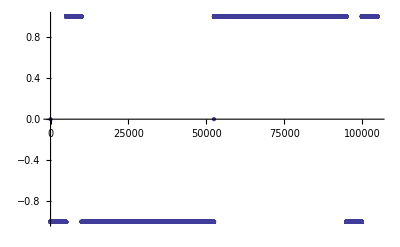

```mathematica
wavname="023";
wavfile=Import[ wavname<>".wav"];
li=wavfile//First//First//First;
rate=SampleRate->(wavfile//First//Last)
len=li//Length
compli=wind[li];
swapList=Range[5000,10000];
extendedCompli=extendedWind[li,swapList];
ListPlot[Im@Fourier[Im@InverseFourier[extendedStep[len,swapList],FourierParameters->{1,-1}],FourierParameters->{1,-1}],PlotRange->All](* 拡張したフィルタ *)
```

```mathematica
spectrumPlot[li_]:=ListLinePlot[Fourier[li,FourierParameters->{1,-1}]//Abs,PlotRange->All]
```

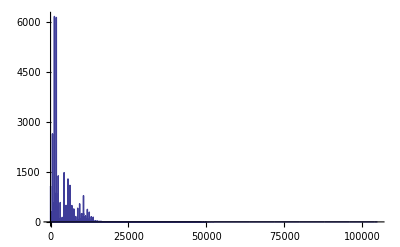

```mathematica
spectrumPlot[compli]
```

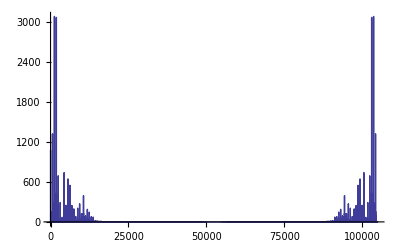

```mathematica
spectrumPlot[Re[compli]]
```

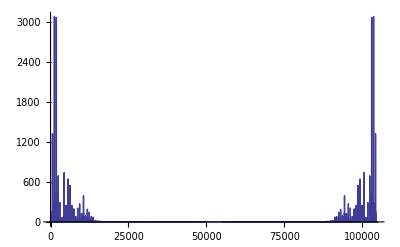

```mathematica
spectrumPlot[Im[compli]]
```

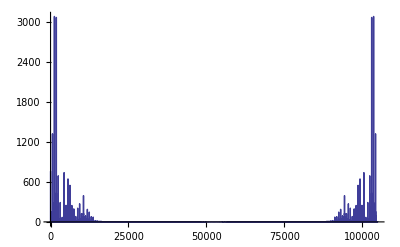

```mathematica
spectrumPlot[Re[ⅇ^(ⅈ π/4)compli]]
```

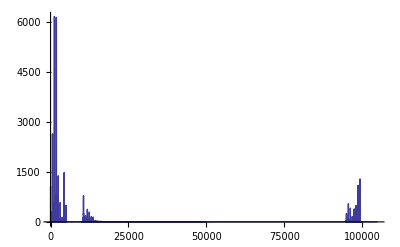

```mathematica
spectrumPlot[extendedCompli]
```

```mathematica
spectrumPlot[Re[extendedCompli]]
```

-Graphics-

```mathematica
spectrumPlot[Im[extendedCompli]]
```

-Graphics-

```mathematica
spectrumPlot[Re[ⅇ^(ⅈ π/4)extendedCompli]]
```

-Graphics-

```mathematica
ListLinePlot[li]
```

-Graphics-

```mathematica
mainRange={20000,20168};
```

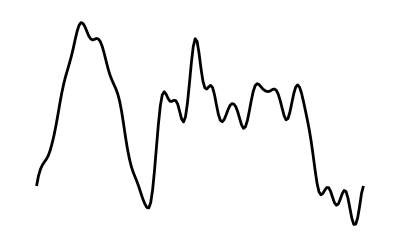

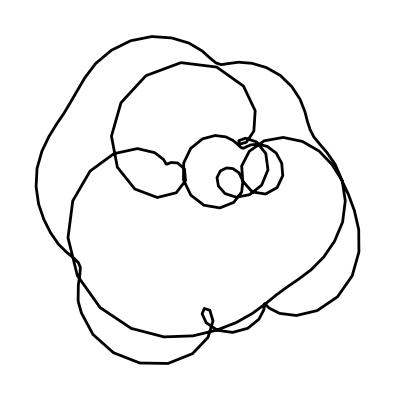

-Graphics-

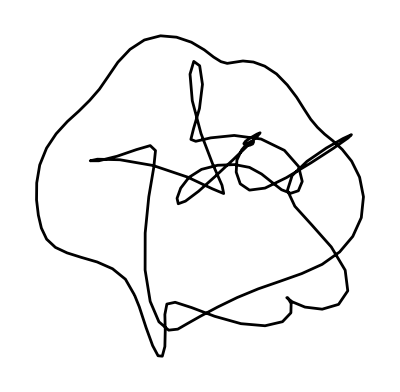

```mathematica
periodiclistlineplot[Re[Take[compli,mainRange]]]
complexlistlineplot[Take[compli,mainRange]]
periodiclistlineplot[Re[Take[extendedCompli,mainRange]]]
complexlistlineplot[Take[extendedCompli,mainRange]]
```